```mathematica
i[x_]:=(3/(8x^3))(x(1+2x^2)Sqrt[1+x^2]-Log[x+Sqrt[1+x^2]])
```

```mathematica
i'[x]//Simplify
```

(3 (-3 x-x^3+2 x^5+3 √(1+x^2) Log[x+√(1+x^2)]))/(8 x^4 √(1+x^2))

```mathematica
γ[x_]:=(1/(9x^2))(#^4i'[#]&)'[x]//Simplify
```

```mathematica
γ[x]
```

x^2/(3 √(1+x^2))

```mathematica
ϵ[x_]:= x^3i[x]//Simplify
```

```mathematica
P[x_]:=(1/3) x^4i'[x]//Simplify
```

```mathematica
(*Subscript[μ, j_][x_]:=3((Subscript[m, j]^4c^5)/(3Pi^2ℏ^3))x^2Sqrt[1+x^2]*)
```

```mathematica
e=Evaluate[(Subscript[A, R] x+Subscript[A, NR] x^(3/5)/.FindFit[Table[{P[x],ϵ[x]},{x,0.001,60,0.001}],Subscript[A, R] x+Subscript[A, NR] x^(3/5),{Subscript[A, R],Subscript[A, NR]},x])/.{x->#}]&
```

0.947353 #1^(3/5)+2.99927 #1&

```mathematica
NumberForm[e[x],18]
```

0.94735296709173 x^(3/5)+2.999273659636282 x

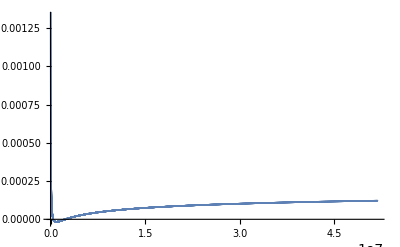

```mathematica
ListPlot[Table[{P[x],(ϵ[x]-e[P[x]])/ϵ[x]},{x,0.01,120,0.01}]]
```

```mathematica
((1-α)/2)^(5/3)+((1+α)/2)^(5/3)//Simplify
```

((1-α)^(5/3)+(1+α)^(5/3))/(2 2^(2/3))

```mathematica
Subscript[ϵ, R][α_]:=x^3(Subscript[λ, n]^3 i[Subscript[λ, n] x]+Subscript[λ, p]^3 i[Subscript[λ, p] x])/.{Subscript[λ, n]->((1+α)/2)^(1/3),Subscript[λ, p]->((1-α)/2)^(1/3)}//Simplify
```

```mathematica
Δϵ=(Subscript[ϵ, R][α]-Subscript[ϵ, R][0])//Simplify
```

3/8 (-2^(1/6) x (1+2^(1/3) x^2) √(2+2^(1/3) x^2)+(x (1+2^(1/3) x^2 (1-α)^(2/3)) √(2+2^(1/3) x^2 (1-α)^(2/3)) (1-α)^(1/3))/2^(5/6)+(x (1+α)^(1/3) (1+2^(1/3) x^2 (1+α)^(2/3)) √(2+2^(1/3) x^2 (1+α)^(2/3)))/2^(5/6)+2 Log[x/2^(1/3)+√(1+x^2/2^(2/3))]-Log[√(1+(x^2 (1-α)^(2/3))/2^(2/3))+(x (1-α)^(1/3))/2^(1/3)]-Log[(x (1+α)^(1/3))/2^(1/3)+√(1+(x^2 (1+α)^(2/3))/2^(2/3))])

```mathematica
Series[Δϵ,{α,0,2}]
```

((2^(5/6) x^5+2^(1/6) x^7) α^2)/(6 (2+2^(1/3) x^2)^(3/2))+O[α]^3

```mathematica
Δϵ/.{α->1}//Simplify
```

3/8 (x √(1+x^2) (1+2 x^2)-2^(1/6) x (1+2^(1/3) x^2) √(2+2^(1/3) x^2)-Log[x+√(1+x^2)]+2 Log[x/2^(1/3)+√(1+x^2/2^(2/3))])

```mathematica
Δϵ/x^3 i[x]/.{α->1,x->1}//N
```

0.111892

```mathematica
Series[i[x],{x,0,2}]
```

1+(3 x^2)/10+O[x]^3

```mathematica
Subscript[ϵ, nr][x_,α_]:=x^3(((1+α)/2)(1+3/10(((1+α)/2)^(1/3)x)^2)+((1-α)/2)(1+3/10(((1-α)/2)^(1/3)x)^2))//Simplify
```

```mathematica
Subscript[Δϵ, nr][x_,α_]:=Subscript[ϵ, nr][x,α]-Subscript[ϵ, nr][x,0]//Simplify
```

```mathematica
Subscript[ϵ, nr][x,0]
```

x^3+(3 x^5)/(10 2^(2/3))

```mathematica
Subscript[Δϵ, nr][x,1]
```

-3/20 (-2+2^(1/3)) x^5

```mathematica
Subscript[ϵ, S][n_]:=n(Subscript[m, N] c^2(1+3/10(n η/n0)^(2/3))+A(n/n0)/2+B(n/n0)^σ/((σ+1)(1+C1(n/n0)^(σ-1))))
```

```mathematica
Subscript[ϵ, S][n0]/n0-Subscript[m, N] c^2/.{A->-122.2,B->65.39,σ->2.112,Subscript[m, N] c^2->938.5,η->0.0438853,C1->0}//Simplify
```

-40.0878+281.55 η^(2/3)

```mathematica
D[Subscript[ϵ, S][n]/n,n]/.{n->n0}//Simplify
```

(5 (A+(2 B (C1+σ))/((1+C1)^2 (1+σ)))+2 c^2 η^(2/3) m_N)/(10 n0)

```mathematica
Subscript[ϵ, S][n0]/n0-Subscript[m, N] c^2
```

A/2+B/((1+C1) (1+σ))-c^2 m_N+c^2 (1+(3 η^(2/3))/10) m_N

```mathematica
9(n^2 D[Subscript[ϵ, S][n]/n,{n,2}]+2n D[Subscript[ϵ, S][n]/n,n])/.{n->n0}//Simplify
```

9 A+(9 B (2 C1^2-C1 (-5+σ) σ+σ (1+σ)))/((1+C1)^3 (1+σ))+3 c^2 η^(2/3) m_N

```mathematica
Solve[{(D[Subscript[ϵ, S][n]/n,n]/.{n->n0}//Simplify)==0,Subscript[ϵ, S][n0]/n0-Subscript[m, N] c^2==BE,(9(n^2 D[Subscript[ϵ, S][n]/n,{n,2}]+2n D[Subscript[ϵ, S][n]/n,n])/.{n->n0}//Simplify)==Subscript[k, 0]},{A,B,σ}]//Simplify
```

{{A→(900 BE^2 C1-60 BE c^2 (2+3 C1) η^(2/3) m_N+9 c^4 C1 η^(4/3) m_N^2+10 k_0 (10 BE-3 c^2 η^(2/3) m_N))/(5 (90 BE+10 k_0-3 c^2 η^(2/3) m_N)),B→-((1+C1) (10 BE-c^2 η^(2/3) m_N) (90 BE (-1+3 C1)+10 (1+C1) k_0+3 c^2 (5-7 C1) η^(2/3) m_N))/(10 (90 BE+10 k_0-3 c^2 η^(2/3) m_N)),σ→(2 (90 BE C1+5 (1+C1) k_0+3 c^2 (1-2 C1) η^(2/3) m_N))/(9 (-1+C1) (10 BE-c^2 η^(2/3) m_N))}}

```mathematica
Subscript[ϵ, S][n0]/n0-Subscript[m, N] c^2/.{A->1.26103*10^-9,B->-1.33881*10^-9,σ->0.689239,C1->0,c^2 Subscript[m, N]->1.50431*10^-10}
```

-3.12468×10^-10+1.50431×10^-10 (1+(3 η^(2/3))/10)

```mathematica
Subscript[ϵ, S][n0]/n0-Subscript[m, N] c^2/.{A->(900 BE^2 C1-60 BE c^2 (2+3 C1) η^(2/3) Subscript[m, N]+9 c^4 C1 η^(4/3) Subscript[m, N]^2+10 Subscript[k, 0] (10 BE-3 c^2 η^(2/3) Subscript[m, N]))/(5 (90 BE+10 Subscript[k, 0]-3 c^2 η^(2/3) Subscript[m, N])),B->-((1+C1) (10 BE-c^2 η^(2/3) Subscript[m, N]) (90 BE (-1+3 C1)+10 (1+C1) Subscript[k, 0]+3 c^2 (5-7 C1) η^(2/3) Subscript[m, N]))/(10 (90 BE+10 Subscript[k, 0]-3 c^2 η^(2/3) Subscript[m, N])),σ->(2 (90 BE C1+5 (1+C1) Subscript[k, 0]+3 c^2 (1-2 C1) η^(2/3) Subscript[m, N]))/(9 (-1+C1) (10 BE-c^2 η^(2/3) Subscript[m, N]))}//Simplify
```

BE